```mathematica
ImageRotate[Import["D:\\Users\\Scott\\Documents\\GitHub\\mousee\\data\\m8\\IMG_0297.jpg"], Right];

(* Recommended starting values for (n1...n4): (1, 0, 0, 1) *)
Manipulate[ImagePerspectiveTransformation[%, {{n1, n2},{n3, n4}}], {n1, 0, 1}, {n2, 0, 1}, {n3, 0, 1}, {n4, 0,5}]
```

```mathematica
f[x_, n_, h_]:=ArcTan[(n x)/h]*180/Pi-ArcTan[((n-1) x)/h]*180/Pi;
alpha[x_, n_, h_] := MaxValue[f[x, n, h], n] ;
N[alpha[1, n, 2]]
```

28.0725

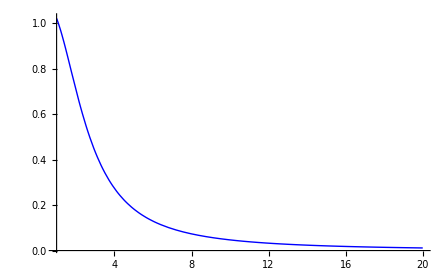

```mathematica
Plot[
f[1, n, 2]/26, 
{n, 1, 20}, 
PlotRange->All,
PlotStyle->{
{Thick, Blue}, 
{Thick, Red}
}, 
AxesOrigin->{1,0}]
```